# Vector Plots and Optimization

## Derek Prince Week 7 APPM 2450 - 003, Fall 2015 Due 9th October, 2015

```mathematica
Clear["Global`*"];
```

## Patrol Cabin Locations

```mathematica
f[x_,y_] = y(x^2-4)+(y^2-1);
```

“The main requirement is that the ground be level where the cabins are to be located.”

#### 1)

```mathematica
gradf[x_,y_] = D[f[x,y],{{x,y}}]
```

{2 x y,-4+x^2+2 y}

#### 2)

Gradien vector field alond with level curves of the surface

```mathematica
vecplot = VectorPlot[gradf[x,y], {x,-7,7},{y,-7,7}, FrameLabel->{"x","y"}];
contplot = ContourPlot[f[x,y], {x,-7,7},{y,-7,7},Contours->10];
```

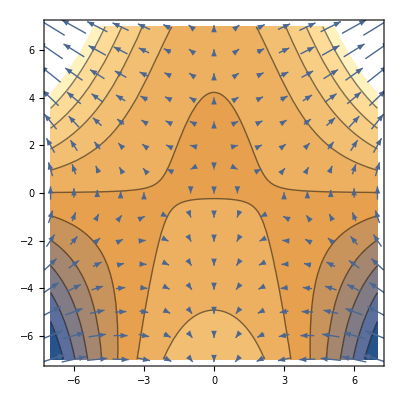

```mathematica
Show[contplot,vecplot]
```

```mathematica
surf = Plot3D[f[x,y], {x,-50,50},{y,-50,50}, ImageSize->Full];
```

#### 3)

Based on this plot, I expect the critical points to be (-2,0), (2,0), and (0,2) because there is a zero vector at each of those points.

#### 4)

```mathematica
cpts = Solve[gradf[x,y] ==0, {x,y}]
```

{{x→-2,y→0},{x→0,y→2},{x→2,y→0}}